24/01/2016

#### Potential

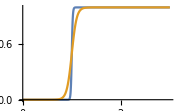

```mathematica
ϕ=1/2(Tanh[(x-X)/d]+Tanh[(x+X)/d]);
Plot[ϕ/.{X->1,d->{0.02,0.1}}//Evaluate,{x,0,3},ImageSize->Small]
```

#### WM Solution to ODE

```mathematica
DSolve[D[r[x],x]+(a ϕ(1+a D[ϕ,x])-(a D[ϕ,{x,2}])/(1+a D[ϕ,x])) r[x]==0,r[x],x]//Simplify
```

{{r[x]→ⅇ^((a^2 (3+2 Cosh[(2 (x-X))/d]+Cosh[(4 X)/d]+2 Cosh[(2 (x+X))/d]))/(4 (Cosh[(2 x)/d]+Cosh[(2 X)/d])^2)) C[1] (Cosh[(2 x)/d]+Cosh[(2 X)/d])^(-2-(a d)/2) (4 a+2 d+d Cosh[(4 x)/d]+4 (a+d) Cosh[(2 x)/d] Cosh[(2 X)/d]+d Cosh[(4 X)/d])}}

```mathematica
DSolve[D[(1/(1+a D[ϕ,x])r[x]),x]+a ϕ r[x]==0,r[x],x];
%//Simplify
```

{{r[x]→ⅇ^((a^2 (3+2 Cosh[(2 (x-X))/d]+Cosh[(4 X)/d]+2 Cosh[(2 (x+X))/d]))/(4 (Cosh[(2 x)/d]+Cosh[(2 X)/d])^2)) C[1] (Cosh[(2 x)/d]+Cosh[(2 X)/d])^(-2-(a d)/2) (4 a+2 d+d Cosh[(4 x)/d]+4 (a+d) Cosh[(2 x)/d] Cosh[(2 X)/d]+d Cosh[(4 X)/d])}}

```mathematica
Plot[ⅇ^((a^2 (3+2 Cosh[(2 (x-X))/d]+Cosh[(4 X)/d]+2 Cosh[(2 (x+X))/d]))/(4 (Cosh[(2 x)/d]+Cosh[(2 X)/d])^2)) (Cosh[(2 x)/d]+Cosh[(2 X)/d])^(-2-(a d)/2) (4 a+2 d+d Cosh[(4 x)/d]+4 (a+d) Cosh[(2 x)/d] Cosh[(2 X)/d]+d Cosh[(4 X)/d])/.{d->1,X->1,a->10},
{x,-3,3}]
```

#### Expansion Close to Wall

```mathematica
Series[ρ,{x,X,2}]//Simplify
```

(ⅇ^(-1/4 a^2 Tanh[(2 X)/d]^2) Sech[(2 X)/d]^((a d)/2) (a+2 d+a Sech[(2 X)/d]^2))/(2 d)-((a ⅇ^(-1/4 a^2 Tanh[(2 X)/d]^2) (16+19 a^2+21 a d+6 d^2+4 (4+3 a^2+6 a d+2 d^2) Cosh[(4 X)/d]+(a^2+3 a d+2 d^2) Cosh[(8 X)/d]) Sech[(2 X)/d]^(5+(a d)/2) Sinh[(2 X)/d]) (x-X))/(32 d^2)+1/(2048 d^3)a ⅇ^(-1/4 a^2 Tanh[(2 X)/d]^2) (-792-1014 a^2-141 a^4-1106 a d-148 a^3 d-300 d^2-65 a^2 d^2-10 a d^3+8 (6 a^4-6 a^3 d-a d (188+d^2)-a^2 (129+5 d^2)-2 (64+29 d^2)) Cosh[(4 X)/d]+4 (-56+19 a^4+36 a^3 d-52 d^2+2 a d (-53+d^2)+a^2 (-2+15 d^2)) Cosh[(8 X)/d]+8 a^2 Cosh[(12 X)/d]+16 a^4 Cosh[(12 X)/d]-32 a d Cosh[(12 X)/d]+48 a^3 d Cosh[(12 X)/d]-48 d^2 Cosh[(12 X)/d]+40 a^2 d^2 Cosh[(12 X)/d]+8 a d^3 Cosh[(12 X)/d]-8 Cosh[(16 X)/d]-2 a^2 Cosh[(16 X)/d]+a^4 Cosh[(16 X)/d]-6 a d Cosh[(16 X)/d]+4 a^3 d Cosh[(16 X)/d]-4 d^2 Cosh[(16 X)/d]+5 a^2 d^2 Cosh[(16 X)/d]+2 a d^3 Cosh[(16 X)/d]) Sech[(2 X)/d]^(8+(a d)/2) (x-X)^2+O[x-X]^3

```mathematica
Series[(1+a/(2d)((1-1/2(x-X)/d)^2+0 Sech[(2X)/d]^2))((1-1/2(x-X)/d)Sech[(2X)/d])^(a d/2)Exp[-(a/2)^2((x-X)/d+1+0Tanh[(2X)/d])^2],{x,X,2}]//FullSimplify//Normal
```

(1+a/(2 d)) ⅇ^(-a^2/4) Sech[(2 X)/d]^((a d)/2)-(a (4+(2 a+d) (a+2 d)) ⅇ^(-a^2/4) (x-X) Sech[(2 X)/d]^((a d)/2))/(8 d^2)+(a (8+4 a^4+12 a^3 d-4 d^2+2 a d (-5+d^2)+a^2 (8+9 d^2)) ⅇ^(-a^2/4) (x-X)^2 Sech[(2 X)/d]^((a d)/2))/(64 d^3)

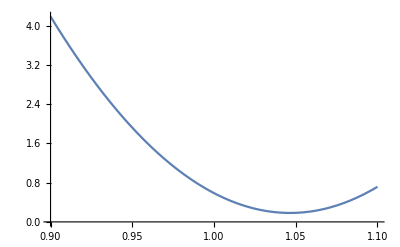

```mathematica
ρX=ⅇ^(-a^2/4) Sech[(2 X)/d]^((a d)/2)((1+a/(2 d)) -(a (4+(2 a+d) (a+2 d))  (x-X))/(8 d^2)+(a (8+4 a^4+12 a^3 d-4 d^2+2 a d (-5+d^2)+a^2 (8+9 d^2))(x-X)^2)/(64 d^3));
Plot[ρX/.{X->1,d->0.1,a->2},{x,0.9,1.1}]
```

#### My Solution

```mathematica
ρ=(1+a/(2d)(Sech[(x-X)/d]^2+Sech[(x+X)/d]^2))(Sech[(x-X)/d]Sech[(x+X)/d])^(a d/2)Exp[-(a/2)^2(Tanh[(x-X)/d]+Tanh[(x+X)/d])^2];
```

```mathematica
pars={d->0.1,X->1,a->{1,10}};
norm=NIntegrate[ρ/.pars,{x,-∞,∞}]
```

{1.65736,0.000314784}

```mathematica
Manipulate[
Plot[(ρ/.{X->1,a->{1,10},d->δ})/norm//Evaluate,{x,0,2},PlotRange->{All,{0,3}}],
{{δ,0.05},0.01,0.1}]
```

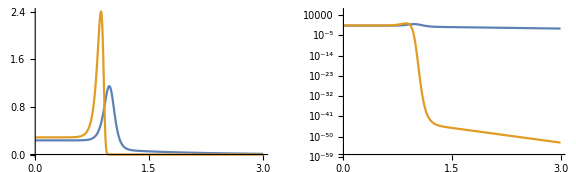

```mathematica
ρlin=Plot[
(ρ/.pars)/norm//Evaluate,{x,0,3},PlotRange->All];
ρlog=LogPlot[(ρ/.pars)/norm//Evaluate,{x,0,3},PlotRange->All];
GraphicsRow[{ρlin,ρlog},ImageSize->Large]
```

#### Simulation

```mathematica
SetDirectory[NotebookDirectory[]];
ρsim=Import["./Pressure/151212X10.0D0.008r50/BHIS_a0.9_X10.0_D0.008_r50_dt0.01.txt","Table"];
ρsimx=Total[ρsim,{1}]/Total[ρsim,{1,2}]/(2/Length[ρsimx]);
xlist=Table[i,{i,9,11,2/Length[ρsimx]}][[2;;]]//N;
simplt=ListPlot[Transpose[{xlist,ρsimx}],Joined->True,Mesh->All];
```

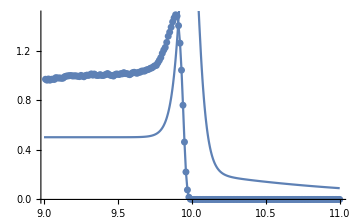

```mathematica
ρadix=ρ/.{d->0.08,X->10,a->0.9};ρadix/=NIntegrate[ρadix,{x,9,11}];
adiplt=Plot[ρadix,{x,9,11},PlotRange->All];
Show[{simplt,adiplt}//Evaluate,ImageSize->Medium]
```

#### Pressure

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

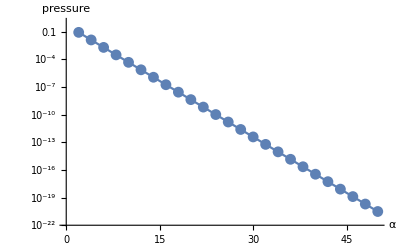

```mathematica
alist=Table[a,{a,0,50,2}];
Plist={#,NIntegrate[a*ρ*ϕ/.{X->1,d->0.1,a->#},{x,0,∞}]}&@alist//Transpose;
ListLogPlot[
Plist,Joined->True,Mesh->All,
AxesLabel->{"α","pressure"}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {35.656}. NIntegrate obtained 0.882711 and 0.000451569 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {35.656}. NIntegrate obtained 0.813563 and 0.0000185417 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

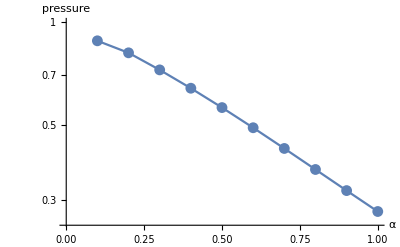

```mathematica
alist=Table[a,{a,0.1,1,0.1}];
Plist={#,NIntegrate[a*ρ*ϕ/.{X->1,d->0.1,a->#},{x,0,∞}]}&@alist//Transpose;
ListLogPlot[
Plist,Joined->True,Mesh->All,
AxesLabel->{"α","pressure"}
]
```

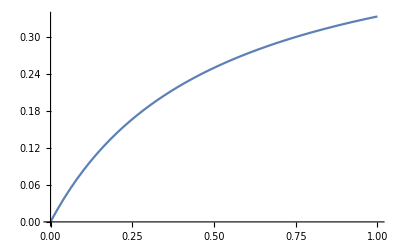

```mathematica
Plot[1/(1/a+2X)/.X->1,{a,0,1}]
```

{1/2 a (Tanh[(x-X)/d]+Tanh[(x+X)/d]),(a d (Tanh[(x-X)/d]+Tanh[(x+X)/d]))/(2 d+a Sech[(x-X)/d]^2+a Sech[(x+X)/d]^2)}

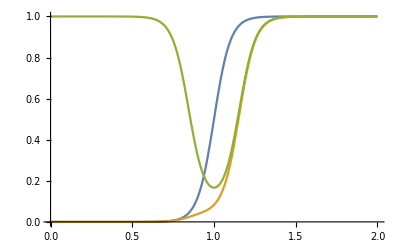

```mathematica
{a ϕ,(a ϕ)/(1+a D[ϕ,x])}//Simplify
Plot[{a ϕ,(a ϕ)/(1+a D[ϕ,x]),1/(1+a D[ϕ,x])}/.{X->1,d->0.1,a->1}//Evaluate,{x,0,2}]
```